>Plot SG sharpness with fixed distance(1) and varying light radius:

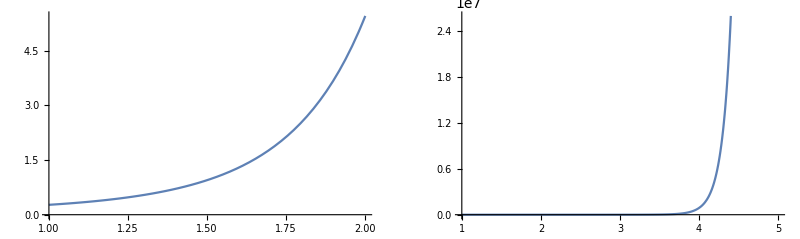

>Plot SG sharpness with fixed light radius(5) and varying distance:

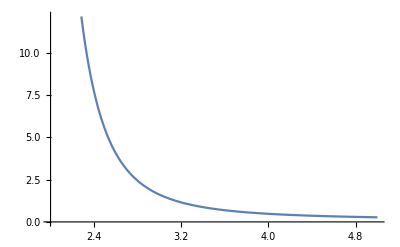

```mathematica
Clear["Global`*"];

Subscript[f, a][λ_,ϵ_]=-2N[π]*N[Log[ϵ/λ]];
DefaultEpsilon=0.1;

Fa[λ_]:=Subscript[f, a][λ,DefaultEpsilon];
InvFa=InverseFunction[Fa];

(*https://neil3d.github.io/assets/pdf/s2013_pbs_epic_notes_v2.pdf Page 12*)
FallOff[r_,d_]:=(Clip[(1-(d/r)^4),{0,1}])^2/(d^2+1);

Print[">Plot SG sharpness with fixed distance(1) and varying light radius:"];
sgSharpness[dist_,lightRadius_]:=InvFa[2π*lightRadius^2/dist^2];
sgSharpnessNew[dist_,lightRadius_]:=InvFa[2π*dist^2]/lightRadius;
{Plot[sgSharpness[1,lightRadius],{lightRadius,1,2}],
Plot[sgSharpness[1,lightRadius],{lightRadius,1,5}]}//GraphicsRow
Print[">Plot SG sharpness with fixed light radius(5) and varying distance:"];
{Plot[sgSharpness[shadingDist,5],{shadingDist,2,5}],
Plot[sgSharpness[shadingDist,5],{shadingDist,0.1,2}]}//GraphicsRow
```

>Plot new sharpness function with fixed light radius(5) and varying distance:

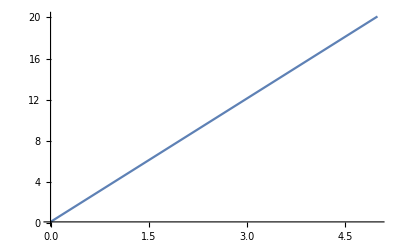

```mathematica
sgSharpnessNew[dist_,lightRadius_]=0.1+(dist/lightRadius)*20;
Print[">Plot new sharpness function with fixed light radius(5) and varying distance:"];
Plot[{sgSharpnessNew[shadingDist,5]},{shadingDist,0,5},PlotRange->Full]
```

```mathematica
G[v_,{p_,λ_,μ_}]:=μ*Exp[λ*(Dot[Normalize[v],Normalize[p]]-1)];
(*All-Frequency Eq(3)*)
G1[θ_,λ_]:=Exp[λ*(Cos[θ]-1)];
sgIntegral[λ_,μ_:1]:=μ*2π*(1-Exp[-2λ])/λ;

B[t_,radius_,a_,b_,c_]:=(a*t^2+b*t+c);

FallOffPercent[radius_,percent_]=FallOff[radius,radius*percent];
sgSharpnessNewPercent[radius_,percent_,d_,e_,f_]=Abs[d*percent^2+e*percent+f]+5;
sgLightFallOff1[radius_,distPercent_,a_,b_,c_,d_,e_,f_]=
sgIntegral[sgSharpnessNewPercent[radius,distPercent,d,e,f],
B[distPercent,radius,a,b,c]];

(*
FindMinimum[NIntegrate[
Abs[FallOffPercent[radius,distPercent]-sgLightFallOff[radius,distPercent,p0,p11,p12,p13,p21,p22,p23,p3]],
{radius,10,1000},{distPercent,0,1},
PrecisionGoal->5,WorkingPrecision->5
],
{p0,1.13},{p11,0},{p12,0},{p13,10},{p21,0},{p22,0},{p23,1/3000},{p3,1}
]
*)

FitRadius=1;

FindMinimum[NIntegrate[
Abs[FallOffPercent[FitRadius,distPercent]-sgLightFallOff1[FitRadius,distPercent,a,b,c,d,e,f]],
{distPercent,0,1},
PrecisionGoal->1,AccuracyGoal->1, Method->"QuasiMonteCarlo",MaxRecursion->2
],
{a,1.13},{b,1},{c,1},{d,1},{e,1},{f,1}
]
```

NIntegrate::inumr: The integrand Abs[-(2 (c+b distPercent+a distPercent^2) (1-ⅇ^(-2 Plus[«3»])) π)/(d distPercent^2+distPercent e+f)+Clip[1-Power[«2»],{0,1}]^2/(1+4 distPercent^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate::inumr: The integrand Abs[-(6.28319 (c+b distPercent+a distPercent^2) (1-ⅇ^(-2 Plus[«3»])))/(d distPercent^2+distPercent e+f)+Clip[1-Power[«2»],{0,1}]^2/(1+4. distPercent^2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.00380209,{a→-0.340146,b→0.0665636,c→0.236471,d→3.79125,e→0.618155,f→1.38885}}

```mathematica
RadiusParams={
{0.791375,-1.89057,1.0872,6.66654,-10.8249,6.76642},
{-0.340146,0.0665636,0.236471,3.79125,0.618155,1.38885},
{0.385139,-0.87285,0.485253,1.80957,0.308354,2.7173},
{0.213239,-0.506706,0.291679,1.83615,2.49729,1.51728}, 
{0.128335,-0.316743,0.187358,2.15074,3.59944,0.786432}};

Print[">Left:Fit Fall Off, Middle: Fit sharpness, Right: Fit Amplitude"]
Manipulate[
{
Plot[{FallOffPercent[radius,percent],
sgLightFallOff1[radius,percent,
RadiusParams[[radius]][[1]],RadiusParams[[radius]][[2]],RadiusParams[[radius]][[3]],
RadiusParams[[radius]][[4]],RadiusParams[[radius]][[5]],RadiusParams[[radius]][[6]]
]
},
{percent,0,1},
PlotStyle->{Green,Blue},
PlotRange->Full],
Plot[sgSharpnessNewPercent[radius,percent,
RadiusParams[[radius]][[4]],RadiusParams[[radius]][[5]],RadiusParams[[radius]][[6]]],
{percent,0,1},
PlotRange->Full],
Plot[B[percent,radius, 
RadiusParams[[radius]][[1]],RadiusParams[[radius]][[2]],RadiusParams[[radius]][[3]]],
{percent,0,1},
PlotRange->Full]
}//GraphicsRow,
{radius,1,5,1}]
```

>Left:Fit Fall Off, Middle: Fit sharpness, Right: Fit Amplitude

```mathematica
Plot3D[FallOffPercent[radius,percent],{radius,10,1000},{percent,0,1}]
```

-Graphics3D-